# Learning Wolfram Language

### Exercises for Section 1 | Starting Out: Elementary Arithmetic

#### 1.1 Compute1+2+3.

```mathematica
1+2+3
```

6

#### 1.2 Add the numbers 1,2,3,4,5.

```mathematica
1+2+3+4+5
```

15

#### 1.3 Multiply the numbers 1, 2, 3, 4, 5.

```mathematica
1*2*3*4*5
```

120

#### 1.4 Compute 5 squared (i . e . 5*5 or 5 raised to the power 2)

```mathematica
5^2
```

25

#### 1.5 Compute 3 raised to the fourth power .

```mathematica
3^4
```

81

#### 1.6 Compute 10 raised to the power 12 (a trillion) .

```mathematica
10^12
```

1000000000000

#### 1.7 Compute 3 raised to the power 7 x8 .

```mathematica
3^(7*8)
```

523347633027360537213511521

#### 1.8 Add parentheses to 4 - 2*3 + 4 to make 14.

```mathematica
(4-2)*(3+4)
```

14

#### 1.9 Compute twenty - nine thousand mutiplied by seventy - three .

```mathematica
29000*73
```

2117000

#### +1.1 Add all integers from - 3 to + 3.

```mathematica
-3+-2+-1+1+2+3
```

0

#### +1.2 Compute 24 divided by 3.

```mathematica
24/3
```

8

#### +1.3 Compute 5 raised to the power 100.

```mathematica
5^100
```

7888609052210118054117285652827862296732064351090230047702789306640625

#### +1.4 Subtract 5 squared from 100

```mathematica
100-(5^2)
```

75

#### +1.5 Multiply 6 by 5 squared, and add 7

```mathematica
(6*(5^2))+7
```

157

#### +1.6 Compute 3 squared minus 2 cubed .

```mathematica
(3^2)-(2^3)
```

1

#### +1.7 Compute 2 cubed times 3 squared

```mathematica
(2^3)*(3^2)
```

72

#### +1.8 Compute "double the sum of eight and negative eleven"

```mathematica
(8-11)*2
```

-6

### Exercises for Section 2 | Introducing Functions

#### 2.1 Compute 7 + 6 + 5 using the function Plus

```mathematica
Plus[7,6,5]
```

18

#### 2.2 Compute 2 x (3 + 4) using Times and Plus

```mathematica
Times[2,Plus[3,4]]
```

14

#### 2.3 Use Max to find the larger of 6x8 and 5x9

```mathematica
Max[Times[6,8],Times[5,9]]
```

48

#### 2.4 Use RandomInteger to generate a random number between 0 and 1000.

```mathematica
RandomInteger[1000]
```

443

#### 2.5 Use Plus and RandomInteger to generate a number between 10 and 20.

```mathematica
Plus[10,RandomInteger[10]]
```

12

#### +2.1 Compute 5 x4x3x2 using Times .

```mathematica
Times[5,4,3,2]
```

120

#### +2.2 Compute 2 - 3 using Subtract

```mathematica
Subtract[2,3]
```

-1

#### +2.3 Compute (8 + 7) + (9 + 2) using Times and Plus

```mathematica
Times[Plus[8,7],Plus[9,2]]
```

165

#### +2.4 Compute (26 - 89)/9 using Subtract and Divide

```mathematica
Divide[Subtract[26,89],9]
```

-7

#### +2.5 Compute 100 - 5^2 using Subtract and Power

```mathematica
Subtract[100,Power[5,2]]
```

75

#### +2.6 Find the larger of 3^5 and 5^3

```mathematica
Max[Power[3,5],Power[5,3]]
```

243

#### +2.7 Multiply 3 and the larger of 4^3 and 3^4

```mathematica
Times[3,Max[Power[4,3],Power[3,4]]]
```

243

#### +2.8 Add two random numbers each between 0 and 1000.

```mathematica
Plus[RandomInteger[1000],RandomInteger[1000]]
```

698

### Exercises for Section 3 | First Look at Lists

#### 3.1 Use Range to create the list {1, 2, 3, 4}

```mathematica
Range[4]
```

{1,2,3,4}

#### 3.2 Make a list of numbers up to 100

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

#### 3.3 Use Range and Reverse to create {4, 3, 2, 1}

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

#### 3.4 Make a list of numbers from 1 to 50 in reverse order .

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

#### 3.5 Use Range, Reverse and Join to create {1, 2, 3, 4, 4, 3, 2, 1}

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

#### 3.6 Plot a list that counts up from 1 to 100, then down to 1.

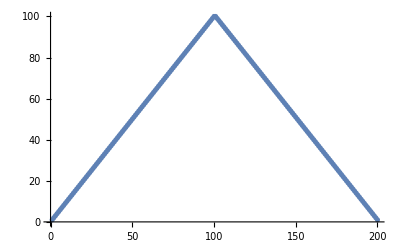

```mathematica
ListPlot[Join[Range[100],Reverse[Range[100]]]]
```

#### 3.7 Use Range and RandomInteger to make a list with a random lenght up to 10.

```mathematica
Range[RandomInteger[10]]
```

{1,2,3}

#### 3.8 Find a simpler form for Reverse[Reverse[Range[10]]]

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

#### 3.9 Find a simpler form to Join[{1, 2}, Join[{3, 4}, {5}]]

```mathematica
Range[5]
```

{1,2,3,4,5}

#### 3.10 Find a simpler form for Join[Range[10], Join[Range[10], Range[5]]]

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

#### 3.11 Find a simpler form for Reverse[Join[Range[20], Reverse[Range[20]]]]

```mathematica
Join[Range[20],Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

#### +3.1 Compute the reverse of the reverse of {1, 2, 3, 4}

```mathematica
Reverse[Reverse[Range[4]]]
```

{1,2,3,4}

#### +3.2 Use Range, Reverse and Join to create the list {1, 2, 3, 4, 5, 4, 3, 2, 1} .

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

#### +3.3 Use Range, Reverse and Join to create {3, 2, 1, 4, 3, 2, 1, 5, 4, 3, 2, 1}

```mathematica
Join[Reverse[Range[3]],Reverse[Range[4]],Reverse[Range[5]]]
```

{3,2,1,4,3,2,1,5,4,3,2,1}

#### +3.4 Plot the list numbers {10, 11, 12, 13, 14}

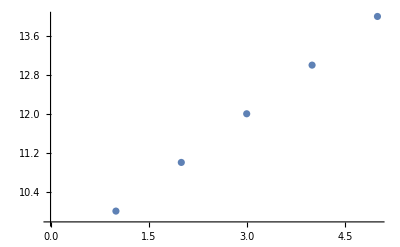

```mathematica
ListPlot[Range[10,14]]
```

### Exercises for Section 4 | Displaying Lists

#### 4.1 Make a bar chart of {1, 1, 2, 3, 5}

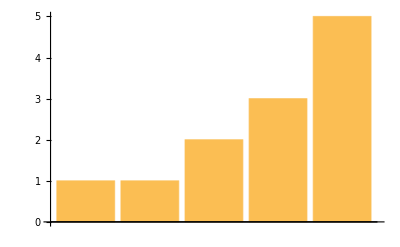

```mathematica
BarChart[{1,1,2,3,5}]
```

#### 4.2 Make a pie chart of numbers from 1 to 10.

```mathematica
PieChart[Range[10]]
```

-Graphics-

#### 4.3 Make a bar chart of numbers counting down from 20 to 1.

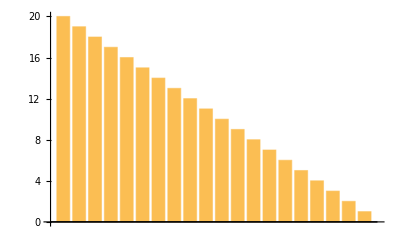

```mathematica
BarChart[Reverse[Range[20]]]
```

#### 4.4 Display numbers from 1 to 5 in a column .

```mathematica
Column[Range[5]]
```

1
2
3
4
5

#### 4.5 Make a number line plot of the squares {1, 4, 9, 16, 25} .

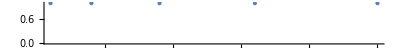

```mathematica
NumberLinePlot[Range[5]^2]
```

#### 4.6 Make a pie chart with 10 identical segments, each of size 1.

```mathematica
PieChart[ConstantArray[1,10]]
```

-Graphics-

#### 4.7 Make a column of pie charts with 1, 2 and 3 identical segments.

```mathematica
Column[{PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]},3]
```

-Graphics-

#### +4.1 Make a list of pie charts with 1, 2 and 3 identical segments .

```mathematica
{PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]}
```

{-Graphics-,-Graphics-,-Graphics-}

#### +4.2 Make a bar chart of the sequence 1, 2, 3, ..., 9, 10, 9, 8, 7, ..., 1.

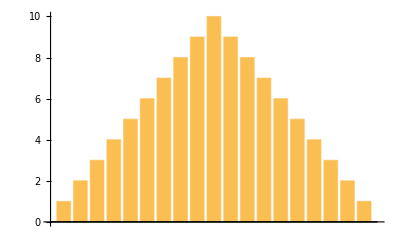

```mathematica
BarChart[Join[Range[10],Reverse[Range[9]]]]
```

#### +4.3 Make a list of pie chart, bar chart and line plot of the numbers from 1 to 10.

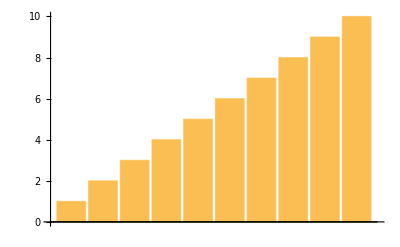
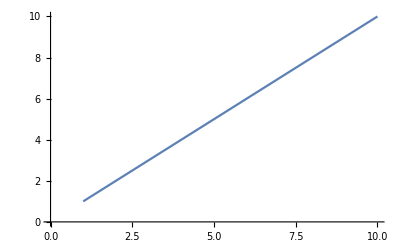
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{PieChart[Range[10]],BarChart[Range[10]],ListLinePlot[Range[10]]}
```

#### +4.4 Make a list of a pie chart and a bar chart of {1, 1, 2, 3, 5, 8, 13, 21, 34, 55}

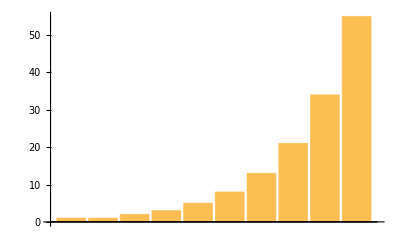
{-Graphics-,-Graphics-}

```mathematica
{PieChart[Fibonacci[Range[10]]],BarChart[Fibonacci[Range[10]]]}
```

#### +4.5 Make a column of two number line plot of {1, 2, 3, 4, 5}

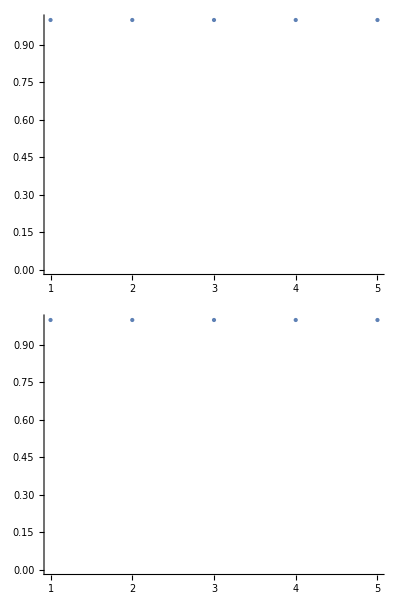

```mathematica
Column[{NumberLinePlot[Range[5]],NumberLinePlot[Range[5]]}]
```

#### +4.6 Mae a number line of fractions 1/2, 1/3, ... through 1/9.

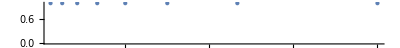

```mathematica
NumberLinePlot[{ConstantArray[1,8]/Range[2,9]}]
```

### Exercises for Section 5 | Operations on Lists

#### 5.1 Make a list of the first 10 squares, in reverse order .

```mathematica
Reverse[Range[10]^2]
```

{100,81,64,49,36,25,16,9,4,1}

#### 5.2 Find the total of the first 10 squares .

```mathematica
Total[Reverse[Range[10]^2]]
```

385

#### 5.3 Make a plot of the first 10 squares, starting at 1.

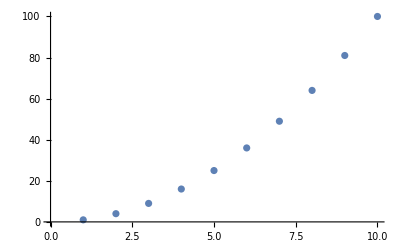

```mathematica
ListPlot[Range[10]^2]
```

#### 5.4 Use Sort, Join and Range to create {1, 1, 2, 2, 3, 3, 4, 4}.

```mathematica
Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

#### 5.5 Use Range and + to make a list of numbers from 10 to 20, inclusive .

```mathematica
Range[0,10]+10
```

{10,11,12,13,14,15,16,17,18,19,20}

#### 5.6 Make a combined list of the first 5 squares and cubes (numbers raised to the power 3), sorted into order .

```mathematica
Sort[Join[Range[5]^2,Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

#### 5.7 Find the number of digits in 2^128.

```mathematica
Length[IntegerDigits[2^128]]
```

39

#### 5.8 Find the first digit of 3^32

```mathematica
First[IntegerDigits[2^32]]
```

4

#### 5.9 Find the first 10 digits in 2^100.

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

#### 5.10 Find the largest digit that appears in 2^20.

```mathematica
Max[IntegerDigits[2^20]]
```

8

#### 5.11 Find how many zeros appear in the digits of 2^1000.

```mathematica
Count[IntegerDigits[2^1000],0]
```

28

#### 5.12 Use Part, Sort and IntegerDigit to find the second - smallest digit in 2^20.

```mathematica
Part[Sort[IntegerDigits[2^20]],2]
```

1

#### 5.13 Make a line plot of the sequence of digits that appear in 2^128.

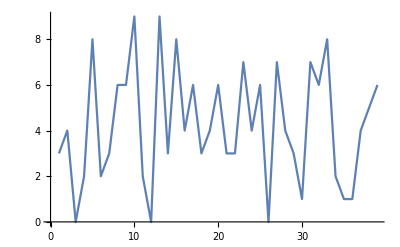

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

#### 5.14 Use Take and Drop to get the sequence 11 through 20 from Range[100].

```mathematica
Take[Drop[Range[100],10],10]
```

{11,12,13,14,15,16,17,18,19,20}

#### +5.1 Make a list of the first 10 multiples of 3.

```mathematica
Range[10]*3
```

{3,6,9,12,15,18,21,24,27,30}

#### +5.2 Make a list of the first 10 squares using only Range and Times .

```mathematica
Times[Range[10],Range[10]]
```

{1,4,9,16,25,36,49,64,81,100}

#### +5.3 Find the last digit of 2^37.

```mathematica
Last[IntegerDigits[2^37]]
```

2

#### +5.4 Find the second-to-last digit of 2^32.

```mathematica
Last[Drop[IntegerDigits[2^32],-1]]
```

9

#### +5.5 Find the sum of all the digits of 3^126.

```mathematica
Total[IntegerDigits[3^126]]
```

234

#### +5.6 Make a pie chart of the sequence of digits that appear in 2^32.

```mathematica
PieChart[IntegerDigits[2^32]]
```

-Graphics-

#### +5.7 Make a list of pie charts for the sequence of digits in 2^20, 2^40, 2^60.

```mathematica
{PieChart[IntegerDigits[2^20]],PieChart[IntegerDigits[2^40]],PieChart[IntegerDigits[2^60]]}
```

{-Graphics-,-Graphics-,-Graphics-}

### Exercises for Section 6 | Making Tables

#### 6.1 Make a list in which the number 1000 is repeated 5 times .

```mathematica
Table[1000,{5}]
```

{1000,1000,1000,1000,1000}

#### 6.2 Make a table of the value of n^3 for n from 10 to 20.

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

#### 6.3 Make a number line plot of the first 20 squares .

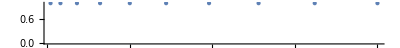

```mathematica
NumberLinePlot[Table[n^2,{n,10}]]
```

#### 6.4 Make a list of the even numbers (2, 4, 6, ...) up to 20.

```mathematica
Table[n*2,{n,10}]
```

{2,4,6,8,10,12,14,16,18,20}

#### 6.5 Use Table to get the same result as Range[10].

```mathematica
Table[n,{n,10}]
```

{1,2,3,4,5,6,7,8,9,10}

#### 6.6 Make a bar chart of the first 10 squares .

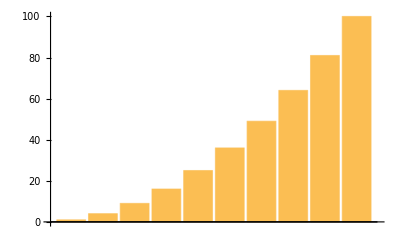

```mathematica
BarChart[Table[n^2,{n,10}]]
```

#### 6.7 Make a table of lists of digits for the first 10 squares.

```mathematica
Table[IntegerDigits[n^2],{n,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

#### 6.8 Make a list line plot of the length of the sequence of digits for each of the first 100 squares.

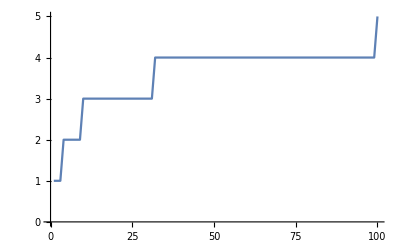

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n,100}]]
```

#### 6.9 Make a table of the first digit of the first 20 squares.

```mathematica
Table[First[IntegerDigits[n^2]],{n,20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

#### 6.10 Make a list line plot of the first digits of the first 100 squares.

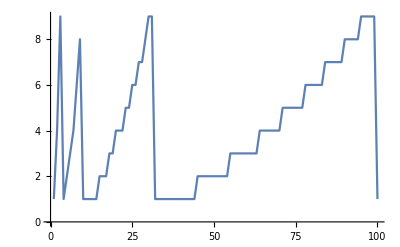

```mathematica
ListLinePlot[Table[First[IntegerDigits[n^2]],{n,100}]]
```

#### +6.1 Make a list of the differences between n^3 and n^2 with n up to 10.

```mathematica
Table[(n^3)-(n^2),{n,10}]
```

{0,4,18,48,100,180,294,448,648,900}

#### +6.2 Make a list of the odd numbers (1, 3, 5, ...) up to 100.

```mathematica
Table[(n*2)-1,{n,50}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

#### +6.3 Make a list of the squares of even numbers up to 100.

```mathematica
Table[(n*2)^2,{n,50}]
```

{4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000}

#### +6.4 Create the list {-3, -2, -1, 0, 1, 2} using Range .

```mathematica
Range[-3,2]
```

{-3,-2,-1,0,1,2}

#### +6.5 Make a list for the numbers n up to 20 in which each element is a column of the value of n, n^2 and n^3.

```mathematica
Table[Column[{n,n^2,n^3}],{n,20}]
```

{1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000}

#### +6.6 Make a list line plot of the last digit of the first 100 squares.

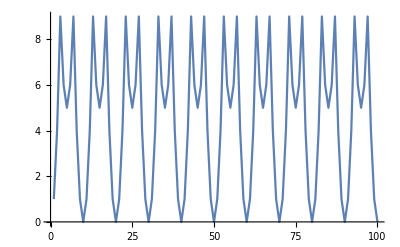

```mathematica
ListLinePlot[Table[Last[IntegerDigits[n^2]],{n,100}]]
```

#### +6.7 Make a list line plot of the first digit of the first 100 multiplies of 3.

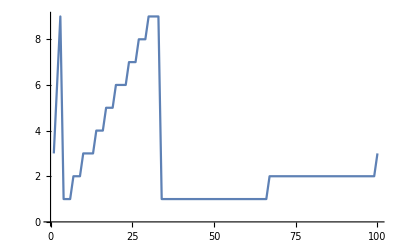

```mathematica
ListLinePlot[Table[First[IntegerDigits[n*3]],{n,100}]]
```

#### +6.8 Make a list line plot of the total of the digits for each number up to 200.

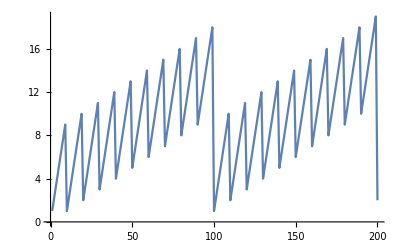

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n]],{n,200}]]
```

#### +6.9 Make a list line plot of the total of the digits for each of the first 100 squares.

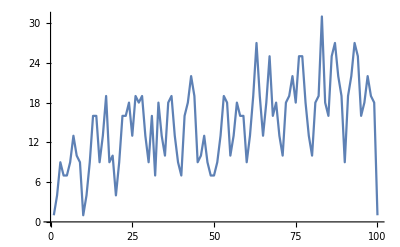

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n^2]],{n,100}]]
```

#### +6.10 Make a number line plot of the numbers 1/n with n from 1 to 20.

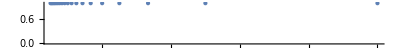

```mathematica
NumberLinePlot[Table[1/n,{n,1,20}]]
```

#### +6.11 Make a line plot of a list of 100 random integers where the nth integer is between 0 and n.

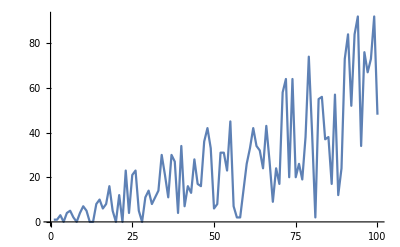

```mathematica
ListLinePlot[Table[RandomInteger[n],{n,100}]]
```

### Exercises for Section 7 | Colors and Styles

#### 7.1 Make a list of red, yellow and green.

```mathematica
{Red,Yellow,Green}
```

{RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

#### 7.2 Make a red, yellow, green column ("traffic light")

```mathematica
Column[{Red,Yellow,Green}]
```

RGBColor[1, 0, 0]
RGBColor[1, 1, 0]
RGBColor[0, 1, 0]

#### 7.3 Compute the negation of the color Orange.

```mathematica
ColorNegate[Orange]
```

RGBColor[0., 0.5, 1.]

#### 7.4 Make a list of color with hues varying from 0 to 1 in steps of 0.02.

```mathematica
Table[Hue[n],{n,0,1,0.02}]
```

{Hue[0.],Hue[0.02],Hue[0.04],Hue[0.06],Hue[0.08],Hue[0.1],Hue[0.12],Hue[0.14],Hue[0.16],Hue[0.18],Hue[0.2],Hue[0.22],Hue[0.24],Hue[0.26],Hue[0.28],Hue[0.3],Hue[0.32],Hue[0.34],Hue[0.36],Hue[0.38],Hue[0.4],Hue[0.42],Hue[0.44],Hue[0.46],Hue[0.48],Hue[0.5],Hue[0.52],Hue[0.54],Hue[0.56],Hue[0.58],Hue[0.6],Hue[0.62],Hue[0.64],Hue[0.66],Hue[0.68],Hue[0.7000000000000001],Hue[0.72],Hue[0.74],Hue[0.76],Hue[0.78],Hue[0.8],Hue[0.8200000000000001],Hue[0.84],Hue[0.86],Hue[0.88],Hue[0.9],Hue[0.92],Hue[0.9400000000000001],Hue[0.96],Hue[0.98],Hue[1.]}

#### 7.8 Make a list of numbers from 0 to 1 in steps of 0.1, each with a hue equal to its value.

```mathematica
Table[{Hue[n],Style[n,Hue[n]]},{n,0,1,0.1}]
```

{{Hue[0.],0.},{Hue[0.1],0.1},{Hue[0.2],0.2},{Hue[0.30000000000000004],0.3},{Hue[0.4],0.4},{Hue[0.5],0.5},{Hue[0.6000000000000001],0.6},{Hue[0.7000000000000001],0.7},{Hue[0.8],0.8},{Hue[0.9],0.9},{Hue[1.],1.}}

### Exercises for Section 8 | Basic Graphics Objects

#### 8.1 Use RegularPolygon to draw a triangle.



```mathematica
Graphics[RegularPolygon[3]]
```

#### 8.2 Make graphics of a red circle.

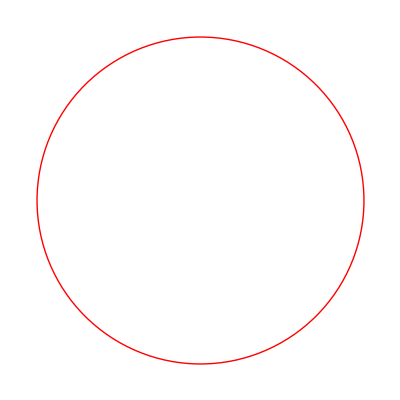

```mathematica
Graphics[Style[Circle[],Red]]
```

#### 8.3 Make a red octagon.

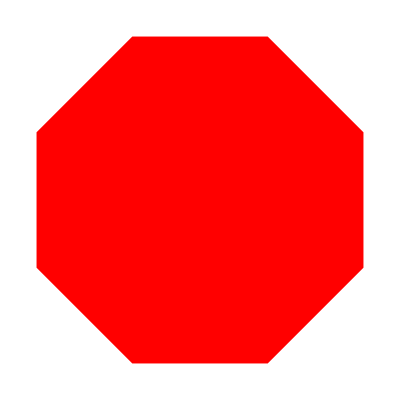

```mathematica
Graphics[Style[RegularPolygon[8],Red]]
```

#### 8.4 Make a list whose elements are disks with hues varying from 0 to 1 in steps of 0.1.


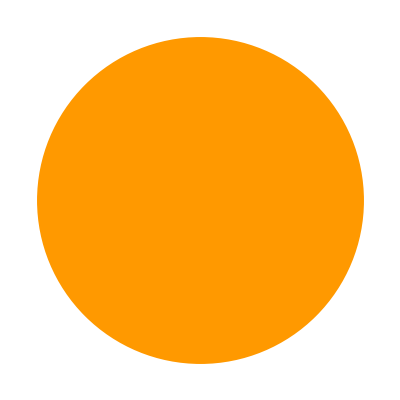
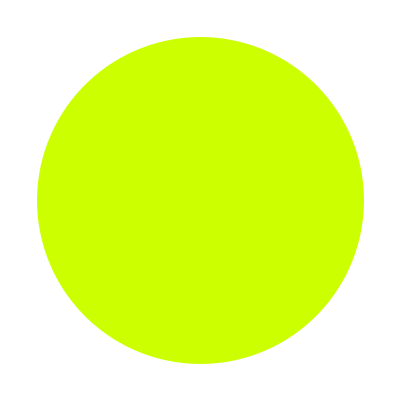
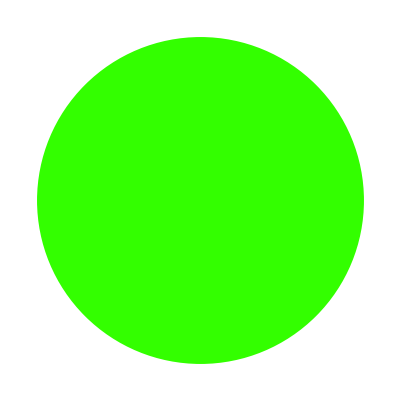
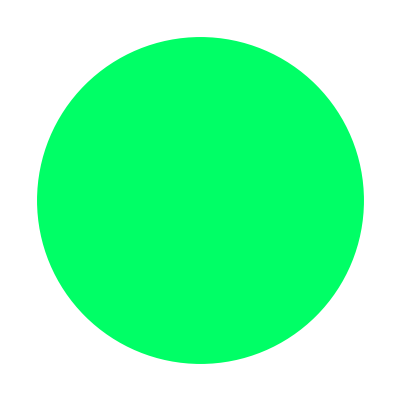
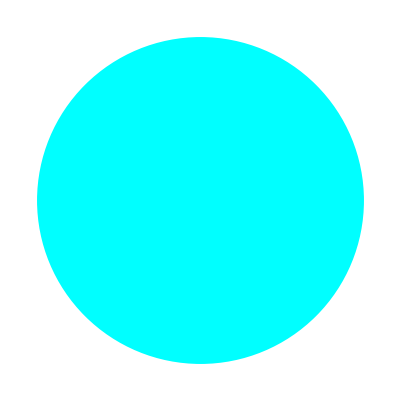
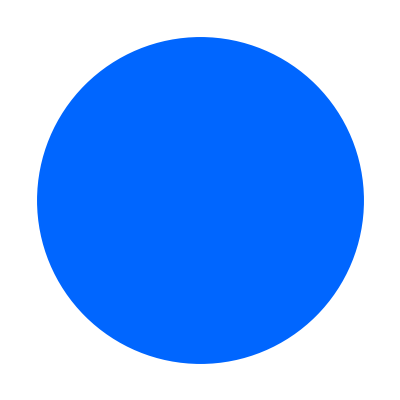
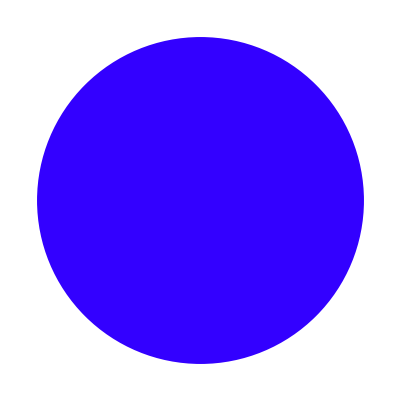
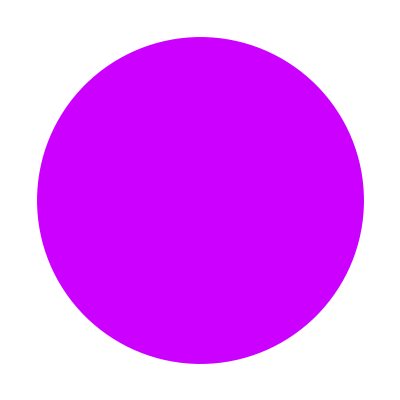
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[Disk[],Hue[n]]],{n,0,1,0.1}]
```

### Exercise for Section 9 | Interactive Manipulation

#### 9.1 Make a Manipulate to show Range[n] with n varying from 0 to 100.

```mathematica
Manipulate[Range[n],{n,0,100}]
```

#### 9.2 Make a Manipulate to plot the whole numbers up to n, where n can range from 5 to 50.

```mathematica
Manipulate[ListPlot[Range[1,n]],{n,5,50}]
```

#### 9.3 Make a Manipulate to show a column of between 1 and 10 copies of x.

```mathematica
Manipulate[Column[Table[x,n]],{n,1,10,1}]
```

#### 9.4 Make a Manipulate to show a disk with a hue varying from 0 to 1.

```mathematica
Manipulate[Graphics[Style[Disk[],Hue[n]]],{n,0,1}]
```

#### 9.5 Make a manipulate to show a disk with red, green and blue color components varying from 0 to 1.

```mathematica
Manipulate[Graphics[Style[Disk[],c]],{c,{Red,Green,Blue}}]
```

#### 9.6 Make a Manipulate to show digit sequences of 4 - digit integers (between 1000 and 9999).

```mathematica
Manipulate[IntegerDigits[n],{n,1000,9999,1}]
```

#### 9.7 Make a Manipulate to create a list of between 5 and 50 equally spaced hues.

```mathematica
Manipulate[Table[Hue[h],{h,0,1,1/n}],{n,5,50,1}]
```

#### 9.8 Make a Manipulate that shows a list of a variable number of hexagons (between 1 and 10), and with variable hues.

```mathematica
Manipulate[Table[Graphics[Style[RegularPolygon[6],Hue[h]]],n],{n,1,10,1},{h,0,1}]
```

#### 9.9 Make a Manipulate that lets you show a regular polygon with between 5 and 20 sides, in red, yellow or blue.

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],c]],{n,5,20,1},{c,{Red,Yellow,Blue}}]
```

#### 9.10 Make a Manipulate that shows a pie chart with a number of equal segments varying from 1 to 10.

```mathematica
Manipulate[PieChart[ConstantArray[1,n]],{n,1,10,1}]
```

#### 9.11 Make a Manipulate that gives a bar chart of the 3 digits in integers from 100 to 999.

```mathematica
Manipulate[BarChart[IntegerDigits[n]],{n,100,999,1}]
```

#### 9.12 Make a Manipulate that shows n random colors, where n can range from 1 to 50.

```mathematica
Manipulate[RandomColor[n],{n,1,50,1}]
```

#### 9.13 Make a Manipulate to display a column of integer powers with bases from 1 to 25 and exponents from 1 to 10.

```mathematica
Manipulate[Column[Range[n]^i],{n,1,20},{i,1,10,1}]
```

#### 9.14 Make a Manipulate of a number line of values of x^n for integer x from 1 to 10, with n varying from 0 to 5.

```mathematica
Manipulate[NumberLinePlot[Range[10]^n],{n,0,5}]
```

#### 9.15 Make a Manipulate to show a sphere that can vary in color from green to red.

```mathematica
Manipulate[Graphics3D[Style[Sphere[],RGBColor[n,1-n,0]]],{n,0,1}]
```

#### +9.1 Make a Manipulate to plot numbers from 1 to 100 raised to powers that can vary between - 1 and + 1.

```mathematica
Manipulate[ListLinePlot[Range[100]^i],{i,-1,1}]
```

#### +9.2 Make a Manipulate to display 1000 at sizes between 5 and 100.

```mathematica
Manipulate[Style[1000,s],{s,5,100}]
```

#### +9.3 Make a Manipulate to show a bar chart with 4 bars, each with a height that can be between 0 and 10.

```mathematica
Manipulate[BarChart[{n,x,y,z}],{n,0,10},{y,0,10},{z,0,10}]
```

### Exercises for Section 10 | Images

#### 10.1 Color negate the result of edge detecting and image . (Use CurrentImage[] or any other image).

```mathematica
img = -Graphics-
```

-Graphics-

```mathematica
ColorNegate[EdgeDetect[img]]
```

-Graphics-

#### 10.2 Use Manipulate to make an interface for blurring and image from 0 to 20.

```mathematica
Manipulate[Blur[img,n],{n,0,20}]
```

#### 10.3 Make a table of the results from edge detecting an image with blurring from 1 to 10.

```mathematica
Table[Blur[EdgeDetect[img],n],{n,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### 10.6 Create a Manipulate to display edges of an image as it gets blurred from 0 to 20.

```mathematica
Manipulate[EdgeDetect[Blur[img,n]],{n,0,20}]
```

### Exercises for Section 11 | Strings and Text

#### 11.1 Join two copies of the string "Hello"

```mathematica
StringJoin["Hello","Hello"]
```

HelloHello

#### 11.2 Make a single string of the whole alphabet, in uppercase.

```mathematica
StringJoin[ToUpperCase[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

#### 11.3 Generate a string of the alphabet in reverse order.

```mathematica
StringReverse[StringJoin[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

#### 11.4 Join 100 copies of the string "AGCT".

```mathematica
StringJoin[ConstantArray["AGCT",100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

#### 11.5 Use StringTake, StringJoin and Alphabet to get “abcdef” .

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

#### 11.7 Make a bar chart of the lengths of the words in "A long time ago, in a galaxy far, far away".

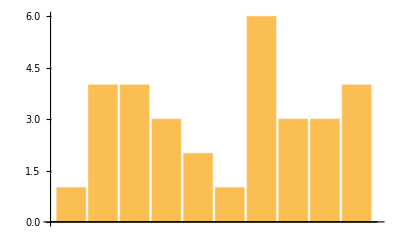

```mathematica
BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away."]]]
```

#### 11.8 Find the string length of the Wikipedia article for "computer".

```mathematica
StringLength[WikipediaData["computer"]]
```

57696

#### 11.9 Find how many words are in the Wikipedia article for “computer”.

```mathematica
Length[TextWords[WikipediaData["computer"]]]
```

8892

#### 11.10 Find the first sentence in the Wikipedia article about “strings”.

```mathematica
First[TextSentences[WikipediaData["strings"]]]
```

String or strings may refer to:

#### 11.11 Make a string from the first letters of all sentences in the Wikipedia article about computers.

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computer"]],1]]
```

AMTATASCESEMTTTCTPP=ATTDBTTT==DTLTTTITIIMTTAAATTTIASIBIAITITIITS=CCATFTTTAEBNH=DHTTTTAB==BTDETTITIRT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAAGTBAIT=TJFCJTHATHTTIWITT=TTDTKIHKNNHPNIMTGFTWISTIS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCIW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETBOBSA=CTITTITCIIA"=AWA=TMH=TQCVSLTTT=ACARPE=AT====M

#### 11.12 Find the maximum word length among English words from WordList[].

```mathematica
Max[StringLength[WordList[]]]
```

23

#### 11.13 Count the number of words in WordList[] that start with “q”.

```mathematica
Count[StringTake[WordList[],1],"q"]
```

194

#### 11.14 Make a line plot of the lengths of the first 1000 words from WordList[]

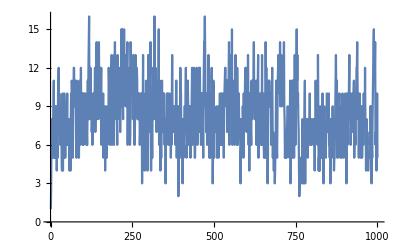

```mathematica
ListLinePlot[StringLength[Take[WordList[],1000]]]
```

#### 11.15 Use StringJoin and Characters to make a word cloud of all letters in the words from WordList[].

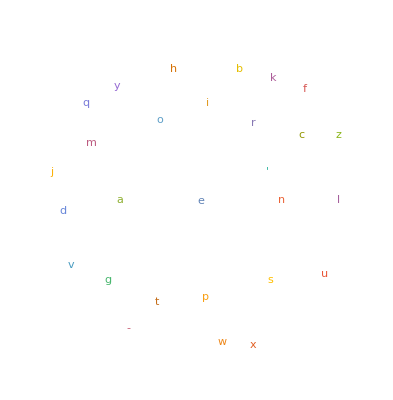

```mathematica
WordCloud[Characters[StringJoin[WordList[]]]]
```

#### 11.16 Use StringReverse to make a word cloud of the last letters in the words from WordList[].

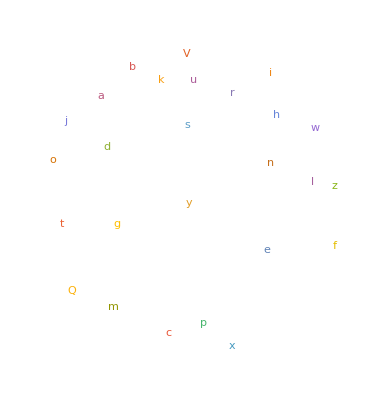

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

#### 11.17 Find the Roman numerals for the year 1959.

```mathematica
RomanNumeral[1959]
```

MCMLIX

#### 11.18 Find the maximum string length of any Roman-numeral year from 1 to 2020.

```mathematica
Max[StringLength[RomanNumeral[Range[2020]]]]
```

13

#### 11.19 Make a word cloud from the first characters of the Roman numerals up to 100.

```mathematica
WordClod[StringTake[RomanNumeral[Range[100]],1]]
```

WordClod[{I,I,I,I,V,V,V,V,I,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,X,X,X,X,X,X,X,X,X,X,C}]

#### 11.20 Use Length to find the length of the Russian alphabet.

```mathematica
Length[Alphabet["Russian"]]
```

33

#### 11.21 Generate the uppercase Greek alphabet.

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

#### 11.22 Make a bar chart of the letter numbers in “wolfram”

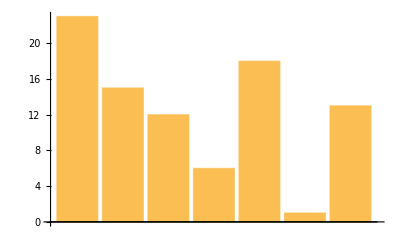

```mathematica
BarChart[LetterNumber["wolfram"]]
```

#### 11.23 Use FromLetterNumber to make a string of 1000 random letters.

```mathematica
StringJoin[FromLetterNumber[Table[RandomInteger[25]+1,1000]]]
```

xqyundcqtfebfucsaghlafrzxkueptkkcvjwmhqsnqyitnilzjaijyvkbtnqfkyecmivkttslvlnjgsuaoidqhiduastrdhrgfxacgsvjnpjmlmhzbkbqccdxyhiarfbupymjllqlplrkxznunypvrpeajvyjtwqmtrkwzrpegpahajepfgebbzsxhglmojtuokvnwcforgqhxmqdqiwhjuqqpfxlcqzevbiezvhmkfanbjjcfzfwyhuigjnezdwxwgulmwlthilccupjztajmtklgicdeecddabpsowxxgdufrfwjstbqkfrogkfmoqisxxlnwsyukowmwmmqjcyjthylvyahxhvwufnrvvjmhtqvgvkddjzkjnuiapbhbqrjzrelrbcubcvanxcbgklnlxmqrdsehkuauuztfsxoftkvuxlcfjjgjivdqhzlnlprlowxxponrdiarkyhbxjtnnbpgngzbeizvmwzrxnltyxydqicfzqgahrhhjeaeynjahlwrcuostyzliongqkunkallrczsfbuzsodcxntpwmvyiexujpldmluwlcdgksosmboryhtdipcqnycbbttrogxlouzsdynibgujshijptfimtxqveuxrmrixgywvziwwxgfbntmjvwjfjczusfrmerlterarzoggwmkknrgprjqsmkwocatqfwkhvutrcuchhpkmthhpdqplfrsqmdxcrzjrdfafsasfmziitcdsbcsvbxozudofmhxnqxytetmipzeuzxvvylrjczsczcbczpkzpukiklhyvpklrlucqdbhodlcqqbwvhggizgkjumgagzvkahzjwkraqxdxcshcwjeharpkptixjoxbxeduylryriqssqzduwmxgalhzrwytvlnxcstpojwkuilybdrkkiuomfswxepxkpqfzzlqkxcpolgitaqfxpgrvlsjosxplsmkmzvvvfuleewclpbirslgqfxczouqkq

#### 11.24 Make a list of 100 random 5-letter stirngs.

```mathematica
Table[StringJoin[Table[FromLetterNumber[RandomInteger[25]+1],5]],100]
```

{dxlhm,scqvc,cptot,eulwu,qlrua,dftym,ccskn,zphsm,tsqns,dxnpj,iijpc,cnemu,zexei,kdnxo,qbsgl,mmdyy,rbnqw,dirkv,vtsaa,iteli,qygth,ptvuo,bhsms,igxkz,tsnet,shwul,zodul,wovdl,iyoqp,yihzt,thrwr,bghqa,tbznq,buyyf,vfuwj,rwzrp,egbhr,ssxzl,vaslb,vqbtr,bdrcc,fgmgw,knhhg,dxgxl,cthbd,nefwx,tvbav,qnrgn,fkaga,hmuym,swtdt,emjiy,bcwen,motdd,mdlvr,erkvw,hqloz,qfebg,pzujl,sqmlg,jsqdd,mzxmy,rfnbh,rhekl,vimjh,iqhdw,hcnvg,iyens,luxne,zcusk,agfvi,xufcs,pdukm,vztfq,zjemu,vjhzw,flxyk,wnfrt,hxctu,rucyz,rjvny,okksl,uuuen,khqdt,eaexm,hkdia,xfrps,coedd,hlexb,tnkdb,wniit,bjbkl,agmrb,aclrk,pspdb,orgdg,nojzt,ddxdc,ltlhw,zmoxg}

#### 11.25 Transliterate “wolfram” into Greek.

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

#### 11.26 Get the Arabic alphabet and transliterate it into English.

```mathematica
Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

#### 11.27 Make a white-on-black size-200 letter “A”.

```mathematica
ColorNegate[Rasterize[Style["A",200]]]
```

-Graphics-

#### 11.28 Use Manipulate to make an interactive selector of size-100 characters from the alphabet, controlled by a slider.

```mathematica
Manipulate[Style[FromLetterNumber[n],100],{n,1,Length[Alphabet[]],1}]
```

#### 11.29 Use Manipulate to make an interactive selector of black-on-white outlines of rasterized size-100 characters from the alphabet, controlled by a menu.

```mathematica
Manipulate[ColorNegate[EdgeDetect[Rasterize[Style[c,100]]]],{c,Alphabet[]}]
```

#### 11.30 Use Manipulate to create a “vision simulator” that blurs a size-200 letter “A” by an amount from 0 to 50.

```mathematica
Manipulate[Blur[Rasterize[Style["A",200]],a],{a,0,50}]
```

#### +11.1 Generate a string of the alphabet followed by the alphabet written in reverse.

```mathematica
StringJoin[StringJoin[Alphabet[]],StringReverse[StringJoin[Alphabet[]]]]
```

abcdefghijklmnopqrstuvwxyzzyxwvutsrqponmlkjihgfedcba

#### +11.3 Find how many sentences are in the Wikipedia article for “computer”.

```mathematica
Length[TextSentences[WikipediaData["computer"]]]
```

449

#### +11.4 Join together without spaces, etc. the words in the first sentence in the Wikipedia article for “strings”

```mathematica
StringJoin[TextWords[First[TextSentences[WikipediaData["strings"]]]]]
```

Stringorstringsmayreferto

#### +11.5 Find the length of the longest word in the Wikipedia article about computers.

```mathematica
Max[StringLength[TextWords[WikipediaData["computers"]]]]
```

25

#### +11.6 Plot the lengths of Roman numerals for numbers up to 2000.

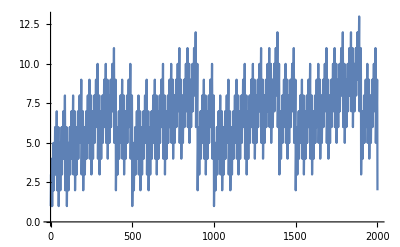

```mathematica
ListLinePlot[StringLength[RomanNumeral[Range[2000]]]]
```

#### +11.7 Generate a string by joining the Roman numerals up to 100.

```mathematica
StringJoin[RomanNumeral[Range[100]]]
```

IIIIIIIVVVIVIIVIIIIXXXIXIIXIIIXIVXVXVIXVIIXVIIIXIXXXXXIXXIIXXIIIXXIVXXVXXVIXXVIIXXVIIIXXIXXXXXXXIXXXIIXXXIIIXXXIVXXXVXXXVIXXXVIIXXXVIIIXXXIXXLXLIXLIIXLIIIXLIVXLVXLVIXLVIIXLVIIIXLIXLLILIILIIILIVLVLVILVIILVIIILIXLXLXILXIILXIIILXIVLXVLXVILXVIILXVIIILXIXLXXLXXILXXIILXXIIILXXIVLXXVLXXVILXXVIILXXVIIILXXIXLXXXLXXXILXXXIILXXXIIILXXXIVLXXXVLXXXVILXXXVIILXXXVIIILXXXIXXCXCIXCIIXCIIIXCIVXCVXCVIXCVIIXCVIIIXCIXC

#### +11.9 Find the maximum string length of the name of any integer up to 1000.

```mathematica
Max[StringLength[IntegerName[Range[1000]]]]
```

27

#### +11.10 Make a list of uppercase size-20 letters of the alphabet in random colors.

```mathematica
Style[ToUpperCase[Alphabet[]],20,RandomColor[]]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

#### +11.11 Make a list of 100 random 5-letter strings with the Russian alphabet.

```mathematica
Table[StringJoin[Table[FromLetterNumber[RandomInteger[25]+1,"Russian"],5]],100]
```

{цшнох,лбпоё,ёлжно,йохпе,лфзёц,оечдг,жпзир,ёопгр,жалиб,бцдсг,снкбн,бавцх,ушкхё,вкубт,фйане,ацмйм,сфшзк,дхуйш,фмрйа,хфкто,пдикм,тлшбу,рблёс,ебихч,ёвжех,кёпое,вкйгл,гншгп,лзхвц,рбрпз,уддда,шдбиу,ииаёц,бееум,дзцум,мфрчф,винсж,швнаш,пижгё,дмвог,метех,кйшоу,цзкеп,днфри,лйагж,чфйгб,лбкнё,дпрсф,гуофн,ииаро,лорпн,анкзв,клдут,ехедй,ётзшп,дмзмп,кнлхт,зфлйж,цёхгё,хггфч,зтфбк,пштчх,оезчш,тесчж,пйбхз,мштно,хдвзб,фиуйм,иоужч,жчупц,вркзж,вцчнд,чёзвп,шмткч,всфшд,зфхтд,емжзё,тйшбб,уфжап,цучач,нфмжс,хчусг,ччнбн,нцчшр,цжатц,йёццу,хеевх,ёвклг,дшопж,вшнсх,ёйбжк,рёрсг,алдлл,утзшр,мпссг,леффе,цфчжт,увнлз,гуйфл,мврйе}